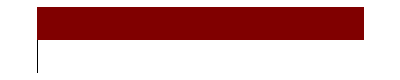

```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"];
Needs["gBRDF`"];
Needs["gUtils`"];
SetDirectory[NotebookDirectory[]];

base=1000;
VanDerCorput[x_,y_]:=Table[FromDigits[{Reverse[IntegerDigits[i,base]],0},y],{i,x}];

RandHalton[x_,y_]:=Block[{step1,step2,step3,Res},step1=Table[RandomReal[{0,10^2}],{y}];
step2=NextPrime[step1,1];
step3=Table[VanDerCorput[x,i],{i,step2}];
Res={Partition[MapThread[##&,step3],Length@step3],step2}];

Halton[x_,y_,z_]:=Block[{step2,step3,Res},step2=z;
step3=Table[VanDerCorput[x,i],{i,step2}];
Res=Partition[MapThread[##&,step3],Length@step3]];
ArrayPlot@RandHalton[1000,2]
```